# Analytical calculations for M = 1 (cont. time limit)

## 1. Computing changes in frequency due to selection

### Introduction

In this notebook, we aim to compute the change in each strategy due to selection <Δx_s^sel>. From the SI, the quantities of interest are

<Δ(x^sel)_CC>=<1/N∑_(i=1)^n s_{i,a}s_{i,d}(ω_i-1)>,                    <Δ(x^sel)_CD>=<1/N∑_(i=1)^n s_{i,a}(1-s_{i,d})(ω_i-1)>,         
<Δ(x^sel)_DC>=<1/N∑_(i=1)^n (1-s_{i,a})s_{i,d}(ω_i-1)>,        <Δ(x^sel)_DD>=<1/N∑_(i=1)^n (1-s_{i,a})(1-s_{i,d})(ω_i-1)>

where ω_i is the expected number of copies of individual i of strategy s due to selection and is given by

ω_i=1+(1-p/2)(f_i/(∑_j f_j)-1/N) ≈1+(1-p/2)(β/N)( π_i-1/N∑_j π_j)=1+(1-p/2)(β/N) Z_i

in the limit of weak selection (β->0). Simplifying expressions in (1),

<Δ(x^sel)_CC>=(1-p/2)(β/N)<s_{i,a}s_{i,d} Z_i>=(1-p/2)(β/N)<Δ(x^sel)_CC>_0,                    <Δ(x^sel)_CD>=(1-p/2)(β/N)<s_{i,a}(1-s_{i,d})Z_i>=(1-p/2)(β/N)<Δ(x^sel)_CD>_0,         
<Δ(x^sel)_DC>=(1-p/2)(β/N)<(1-s_{i,a})s_{i,d}Z_i>=(1-p/2)(β/N)<Δ(x^sel)_DC>_0,        <Δ(x^sel)_DD>=(1-p/2)(β/N)<(1-s_{i,a})(1-s_{i,d})Z_i>=(1-p/2)(β/N)<Δ(x^sel)_DD>_0

where, for <(Δx^sel)_s>_0, the averages are taken over the stationary distribution in the neutral state.

### Defining payoffs

The general payoff function for M = 1 is given by

π_i=-s_{i,a}(b-c)+1/2 ∑_(l=1)^n (b h_i h_l (s_{l,a}-s_{l,d})+b (s_{l,a}+s_{l,d})-c h_i h_l (s_{i,a}-s_{i,d})-c (s_{i,a}+s_{i,d}))+(b-c) s_{i,a}

Thought not required in the calculation, we first define the payoff function for each strategy so that we can simplify the expressions more easily. Note that we use small n instead of N to avoid confusion with the Mathematica function N.

```mathematica
Clear["Global`*"]
```

```mathematica
πgeneral[i_]:= -(Subscript[s, {i,a}])(b-c) + 1/2 ∑_(l=1)^n ExpandAll[(-c (Subscript[s, {i,a}]+Subscript[s, {i,d}])+b  (Subscript[s, {l,a}]+Subscript[s, {l,d}])-c Subscript[h, i] Subscript[h, l](Subscript[s, {i,a}]-Subscript[s, {i,d}])+b Subscript[h, i] Subscript[h, l] (Subscript[s, {l,a}]-Subscript[s, {l,d}]))]
πstrat[i_,sia_,sid_]:= (*sia,sid∈{0,1} to indicate strategy*)-(sia)(b-c) + 1/2 ∑_(l=1)^n ExpandAll[(-c (sia+sid)+b  (Subscript[s, {l,a}]+Subscript[s, {l,d}])-c Subscript[h, i] Subscript[h, l](sia-sid)+b Subscript[h, i] Subscript[h, l] (Subscript[s, {l,a}]-Subscript[s, {l,d}]))]
```

```mathematica
πCC[i_]:=πstrat[i,1,1]
πCD[i_]:=πstrat[i,1,0] 
πDC[i_]:=πstrat[i,0,1]
πDD[i_]:=πstrat[i,0,0]
```

We also define the quantity Z_i (see above):

```mathematica
Z[πstrat_,i_,n_]:=πstrat[i]-1/n∑_(j=1)^n πgeneral[j]//ExpandAll
```

The strategy-specific payoffs are

```mathematica
πCC[i]
πCD[i]
πDC[i]
πDD[i]
```

-b+c+1/2 ∑_(l=1)^n (-2 c+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

-b+c+1/2 ∑_(l=1)^n (-c-c h_i h_l+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

1/2 ∑_(l=1)^n (-c+c h_i h_l+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

1/2 ∑_(l=1)^n (b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

### Defining rules

Next, we define some rules to simplify the summations:

```mathematica
(*rules for initial simplification*)
sumRule=Sum[expr1_,iter_]+Sum[expr2_,iter_]:>Sum[expr1+expr2,iter];
prodRule=Sum[expr1_,iter1_]*Sum[expr2_,iter2_]:>Sum[expr1*expr2,iter1,iter2];
revSumRule=Sum[expr1_+expr2_,iter_]:> Sum[expr1,iter]+Sum[expr2,iter];
constRule=Sum[c_?NumericQ  expr_,iter_]:>c Sum[expr,iter];
distRule=a_(b_+c_):>a*b+a*c;
dist2Rule=s_Subscript(b_+c_):>s*b+s*c;

miscRule=s_Subscript Sum[expr_,iter_]:> Sum[s*expr,iter];
squareRule = s_Subscript^2:>s;
unbracketRule=Sum[expr_,{i_,1,n}]:> n expr;

(*rules for collecting terms*)
mergeRule=a_ s1_Subscript s2_Subscript+b_ s1_Subscript s2_Subscript:> (FullSimplify[a+b])s1 s2;
```

### Simplifying expressions

To make calculations easier, we will first compute terms in (1) divided by (1-p/2)(β/N):

```mathematica
expandBracket[bracket_]:=ExpandAll[bracket]/.revSumRule/.constRule/.distRule//.miscRule//.distRule //.squareRule//.sumRule//.unbracketRule
```

```mathematica
xCCbracket:=expandBracket[Subscript[s, {i,a}] Subscript[s, {i,d}] Z[πCC,i,n]] // FullSimplify//ExpandAll
xCDbracket:=expandBracket[Subscript[s, {i,a}](1-Subscript[s, {i,d}])Z[πCD,i,n]] //FullSimplify//ExpandAll
xDCbracket:=expandBracket[(1-Subscript[s, {i,a}])Subscript[s, {i,d}] Z[πDC,i,n]]// FullSimplify//ExpandAll
xDDbracket:=expandBracket[(1-Subscript[s, {i,a}])(1-Subscript[s, {i,d}])Z[πDD,i,n]]  // FullSimplify//ExpandAll
```

#### Simplifying the CC term

First, we define rules for relabeling quantities that are equivalent (note that the order of substitution matters here).

```mathematica
subCC1={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subCC4={};
subCC2={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}] };
subCC3={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y)}; (*see the SI for definitions of y, z, g, h*)
subCC4={Subscript[s, {i,a}] Subscript[s, {i,d}] -> 1/4};
```

Then we can simplify the expression for CC as:

```mathematica
xCCbracket2=xCCbracket//.distRule//.subCC1//.subCC2//.subCC3//.subCC4 //FullSimplify
```

((b+c (-1+n)) (-1+n) (-1+y))/(4 n)

In the limit n→∞, we can further simplify this expression:

```mathematica
xCCbracket3=FullSimplify[xCCbracket//.distRule//.subCC1//.subCC2//.subCC3//.subCC4 ]/.{n-1->n}/.{b+c n->c n}
```

1/4 c n (-1+y)

#### Simplifying the CD term

```mathematica
subCD5={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subCD6={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		(*Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],*)(*triplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}](*triplet*)};
subCD7={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y),
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y))};
subCD8={Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y)};
subCD9={Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z,Subscript[s, {i,a}]->1/2};
```

```mathematica
xCDbracket2=FullSimplify[xCDbracket]//.distRule//.subCD5//.subCD6//.subCD7//.subCD8//.subCD9//FullSimplify
```

((-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z)))/(4 n)

```mathematica
(*infinit population limit*)
xCDbracket3=FullSimplify[xCDbracket//.distRule//.subCD5//.subCD6//.subCD7//.subCD8//.subCD9]/.{n-1->n,n-2->n}/.{g_-g_ n+h_ n+z_->-g n+h n}//FullSimplify
```

1/4 n (b (g-h)+c (h-z))

#### Simplifying the DC term

```mathematica
subDC10={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]}; (*same as subCD5*)
subDC11={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]->Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}],(*duplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}](*triplet*)};
subDC12={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y),Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y))};
subDC13={Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4,Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n y)};
subDC14={Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z,Subscript[s, {i,d}]->1/2};
```

```mathematica
(*simplify*)
xDCbracket2=FullSimplify[xDCbracket]//.distRule//.subDC10//.subDC11//.subDC12//.subDC13//.subDC14//FullSimplify
```

-((-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z)))/(4 n)

```mathematica
(*infinit population limit*)xDCbracket3=FullSimplify[xDCbracket//.distRule//.subDC10//.subDC11//.subDC12//.subDC13//.subDC14]/.{n-1->n,n-2->n}/.{g_-g_ n+h_ n+z_->-g n+h n}//FullSimplify
```

1/4 n (b (-g+h)+c (-h+z))

#### Simplifying the DD term

```mathematica
(*we combine the simplifications from CD and DC*)
subDD15={Subscript[h, j] Subscript[h, l] Subscript[s, {j,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {j,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[h, i] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[h, i] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y),Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n y),
		Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4};
subDD16={Subscript[s, {j,a}]->1/2,Subscript[s, {j,d}]->1/2};
```

```mathematica
(*simplify*)
xDDbracket2=FullSimplify[xDDbracket]//.distRule//.subCD5//.subCD6//.subDC11//.subCD7//.subDD15//.subDD16//FullSimplify
```

-((b+c (-1+n)) (-1+n) (-1+y))/(4 n)

```mathematica
(*infinit population limit*)
xDDbracket3=FullSimplify[xDDbracket//.distRule//.subCD5//.subCD6//.subDC11//.subCD7//.subDD15//.subDD16]/.{n-1->n,n-2->n}/.{b+c n->c n}//FullSimplify
```

-1/4 c n (-1+y)

### Summary

In the continuous time / large population limit, we have the following expressions for <Δx_CD^sel>_0=<Δ(x^sel)_s>/(β/N):

```mathematica
Print["<Δx_CC^sel>_0= ",xCCbracket3,",  <Δx_CD^sel>_0= ",xCDbracket3,",  <Δx_DC^sel>_0 = ",xDCbracket3,",  <Δx_DD^sel>_0 = ",xDDbracket3]
```

<Δx_CC^sel>_0= 1/4 c n (-1+y),  <Δx_CD^sel>_0= 1/4 n (b (g-h)+c (h-z)),  <Δx_DC^sel>_0 = 1/4 n (b (-g+h)+c (-h+z)),  <Δx_DD^sel>_0 = -1/4 c n (-1+y)

## 2. Computing y, z, g, h in the continuous time limit [for p < 1]

To simplify the above expressions, we need to compute the quantities y, z, g, and h as defined in the SI.

### Define functions related to coalescence time

```mathematica
ρ[τ_,p_]:=Exp[-τ]
ρ2[τ3_,τ2_]:=3*Exp[-3*τ3]Exp[-τ2]
```

### Compute y

```mathematica
ytau[μ_,τ_,p_]:=1/2 (1+ⅇ^(-μ τ))(*from the SI*)
y[μ_,p_]:=Integrate[ytau[μ,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
```

We will also define a function to compute the integrals more quickly :

```mathematica
yeval[μ_,ν_]=y[μ,p];
ycalc[n_,u_,v_]=y[μ,p]/.{μ->n*u};
```

```mathematica
Print["y = ",yeval[μ,ν]," or ",ycalc[n,u,v]]
```

y = (2+μ)/(2+2 μ) or (2+n u)/(2+2 n u)

### Compute z

```mathematica
ztau[ν_,τ_,p_]:=ⅇ^(-ν τ)
z[ν_,p_]:=Integrate[ztau[ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
```

```mathematica
zeval[μ_,ν_]=z[ν,p]// FullSimplify;
zcalc[n_,u_,v_]=z[ν,p]/.{ν->n*v} // FullSimplify;
```

```mathematica
Print["z = ",zeval[μ,ν]," or ",zcalc[n,u,v]]
```

z = 1/(1+ν) or 1/(1+n v)

### Compute g

```mathematica
gtau[μ_,ν_,τ_,p_]:=ytau[μ,τ,p]*ztau[ν,τ,p]
g[μ_,ν_,p_]:=Integrate[gtau[μ,ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
```

```mathematica
geval[μ_,ν_]=g[μ,ν,p] // FullSimplify;
gcalc[n_,u_,v_]=g[μ,ν,p]/.{ν->n*v,μ->n*u}// FullSimplify;
```

```mathematica
Print["Check: g(τ) = ",gtau[μ,ν,τ,p]]
Print["g = ",geval[μ,ν]," or ",gcalc[n,u,v]]
```

Check: g(τ) = 1/2 ⅇ^(-ν τ) (1+ⅇ^(-μ τ))

g = 1/2 (1/(1+ν)+1/(1+μ+ν)) or 1/2 (1/(1+n v)+1/(1+n (u+v)))

### Compute h

```mathematica
htau[μ_,ν_,τ3_,τ2_,p_]:=1/3(ytau[μ,τ3,p]*ztau[ν,τ3+τ2,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ3,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ3+τ2,p])
h[μ_,ν_,p_]:=Integrate[htau[μ,ν,τ3,τ2,p]*ρ2[τ3,τ2], {τ3,0,Infinity},{τ2,0,Infinity}][[1]]
```

```mathematica
heval[μ_,ν_]=h[μ,ν,p] // FullSimplify//Apart; (*slow*)
hcalc[n_,u_,v_]=h[μ,ν,p]/.{ν->n*v,μ->n*u} // FullSimplify// Apart;
```

```mathematica
Print["Check: h(τ_3,τ_2) = ",htau[μ,ν,τ3,τ2,p]]
Print["h = ",heval[μ,ν]," or ",hcalc[n,u,v]]
```

Check: h(τ_3,τ_2) = 1/3 (1/2 ⅇ^(-ν (τ2+τ3)) (1+ⅇ^(-μ τ3))+1/2 ⅇ^(-ν τ3) (1+ⅇ^(-μ (τ2+τ3)))+1/2 ⅇ^(-ν (τ2+τ3)) (1+ⅇ^(-μ (τ2+τ3))))

h = (3+μ)/(2 (2+μ) (1+ν))+1/(4 (1+μ+ν))-(μ (3+μ))/(4 (1+μ) (2+μ) (3+μ+ν)) or (3+n u)/(2 (2+n u) (1+n v))+1/(4 (1+n u+n v))-(n u (3+n u))/(4 (1+n u) (2+n u) (3+n u+n v))

### Compute theoretical predictions and export data

We compute the values of y, z, g, h for various values of v

```mathematica
Clear[n,β,p,u,v,params];
params={n->40,u->0.001,β->0.001};

(*generate a list of vs finer than the sims*)
vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2/2}];

(*compute y,z,g,h for each v*)
data=Flatten[
Table[{u/.params,v,
ycalc[n,u,v]/.params,zcalc[n,u,v]/.params,gcalc[n,u,v]/.params,hcalc[n,u,v]/.params},
{v,vs}],
0]; (*flatten into a data table*)
headers={"u","v","y","z","g","h"};
data=Prepend[data,headers];

filename="~/.julia/dev/CooperationPolarization2/analytics/calc_data_yzgh.csv"; (*change as needed*)
Export[filename,data]
```

~/.julia/dev/CooperationPolarization2/analytics/calc_data_yzgh.csv

```mathematica
data // MatrixForm
```

(u | v | y | z | g | h
0.001 | 0.001 | 0.980769 | 0.961538 | 0.943732 | 0.94327
0.001 | 0.00149535 | 0.980769 | 0.943562 | 0.926403 | 0.925735
0.001 | 0.00223607 | 0.980769 | 0.9179 | 0.901646 | 0.900695
0.001 | 0.0033437 | 0.980769 | 0.88203 | 0.867001 | 0.865677
0.001 | 0.005 | 0.980769 | 0.833333 | 0.819892 | 0.818105
0.001 | 0.00747674 | 0.980769 | 0.769782 | 0.758284 | 0.755968
0.001 | 0.0111803 | 0.980769 | 0.690983 | 0.681691 | 0.678841
0.001 | 0.0167185 | 0.980769 | 0.599254 | 0.59224 | 0.588946
0.001 | 0.025 | 0.980769 | 0.5 | 0.495098 | 0.491551
0.001 | 0.0373837 | 0.980769 | 0.400746 | 0.397584 | 0.394041
0.001 | 0.0559017 | 0.980769 | 0.309017 | 0.30713 | 0.303843
0.001 | 0.0835925 | 0.980769 | 0.230218 | 0.229168 | 0.22632
0.001 | 0.125 | 0.980769 | 0.166667 | 0.166115 | 0.163792
0.001 | 0.186919 | 0.980769 | 0.11797 | 0.117693 | 0.115891
0.001 | 0.279508 | 0.980769 | 0.0820995 | 0.0819651 | 0.0806223
0.001 | 0.417963 | 0.980769 | 0.0564382 | 0.0563746 | 0.0554045
0.001 | 0.625 | 0.980769 | 0.0384615 | 0.038432 | 0.0377472)

The critical threshold (b/c)* for CD to be favored / DC to be disfavored can be plotted as follows:

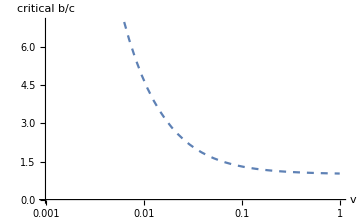

```mathematica
params={β->0.001,u->0.001,n->40};
expressions={ (zcalc[n,u,v]- hcalc[n,u,v])/(gcalc[n,u,v]- hcalc[n,u,v])}/.params;
LogLinearPlot[expressions,{v,0,1},PlotRange->{0,7},AxesLabel->{"v","critical b/c"},ImageSize->Medium,PlotStyle->Dashed]
```

Solve the condition for ν = N*v:

```mathematica
rules2 ={d_?NumericQ+μ->d,d_?NumericQ+f_?NumericQ μ->d,d_?NumericQ c+f_?NumericQ c μ->d c,d_+f_?NumericQ b c μ->d};
```

```mathematica
sol =Solve[b/c==(zeval[μ,ν]-heval[μ,ν])/(geval[μ,ν]-heval[μ,ν]) // FullSimplify, ν];
ν/.sol[[2]]//FullSimplify;
FullSimplify[ν/.sol[[2]]]//.rules2
```

(-2 b+3 c+√(4 b^2-3 c^2))/(2 (b-c))

```mathematica
(*with parameters in our simulation*)
(-2 b+3 c+√(4 b^2-3 c^2))/(2 (b-c) n)/.{b->1,c->0.2,n->40}
```

0.00890268

### Summary: y, z, g, h for p < 1

In summary we have

```mathematica
yeval[μ,ν]
zeval[μ,ν]
geval[μ,ν]
heval[μ,ν]
```

(2+μ)/(2+2 μ)

1/(1+ν)

1/2 (1/(1+ν)+1/(1+μ+ν))

(3+μ)/(2 (2+μ) (1+ν))+1/(4 (1+μ+ν))-(μ (3+μ))/(4 (1+μ) (2+μ) (3+μ+ν))

## 3. Computing strategy frequencies

### Computing the full bracketed terms

We define the following functions to compute the original bracketed terms in (1):

```mathematica
Clear[nn,ββ,pp,bb,cc,μ,μμ,ν,νν];
ΔxCC[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=1/nn xCCbracket3/.{n->nn,b->bb,c->cc,y->yeval[μ,ν]};
ΔxCD[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=1/nn xCDbracket3/.{n->nn,b->bb,c->cc,z->zeval[μ,ν],g-> geval[μ,ν],h-> heval[μ,ν]};
ΔxDC[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=1/nn xDCbracket3/.{n->nn,b->bb,c->cc,z->zeval[μ,ν],g-> geval[μ,ν],h->heval[μ,ν]};
ΔxDD[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=1/nn xDDbracket3/.{n->nn,b->bb,c->cc,y-> yeval[μ,ν]};
```

The full expressions are

```mathematica
FullSimplify[ΔxCC[n,b,c,β,p,μ,ν]] 
FullSimplify[ΔxCD[n,b,c,β,p,μ,ν]]
FullSimplify[ΔxDC[n,b,c,β,p,μ,ν]] 
FullSimplify[ΔxDD[n,b,c,β,p,μ,ν]]
```

-(c μ)/(8+8 μ)

(b μ ν (2+μ+ν)-c μ (3+μ^2+2 μ (2+ν)+ν (3+ν)))/(8 (1+μ) (1+ν) (1+μ+ν) (3+μ+ν))

(μ (-b ν (2+μ+ν)+c (3+μ^2+2 μ (2+ν)+ν (3+ν))))/(8 (1+μ) (1+ν) (1+μ+ν) (3+μ+ν))

(c μ)/(8+8 μ)

In the limit μ -> 0, we have

```mathematica
rules={d_?NumericQ+μ->d,d_?NumericQ+d_ μ->d,d_?NumericQ + μ^2-> d,d_?NumericQ +f_?NumericQ μ*k_-> d};
FullSimplify[ΔxCC[n,b,c,β,p,μ,ν]]//.rules
FullSimplify[ΔxCD[n,b,c,β,p,μ,ν]]//.rules
FullSimplify[ΔxDC[n,b,c,β,p,μ,ν]]//.rules
FullSimplify[ΔxDD[n,b,c,β,p,μ,ν]]//.rules
```

-(c μ)/8

(b μ ν (2+ν)-c μ (3+ν (3+ν)))/(8 (1+ν)^2 (3+ν))

(μ (-b ν (2+ν)+c (3+ν (3+ν))))/(8 (1+ν)^2 (3+ν))

(c μ)/8

### Plot changes due to selection

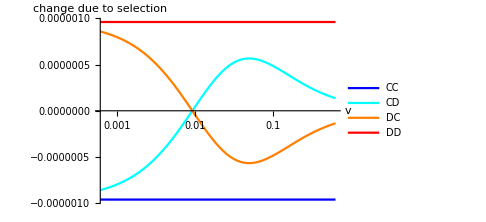

```mathematica
Clear[nn,ββ,pp,bb,cc,μμ,νν];
nn=40;uu=0.001;pp=0;ββ=0.001;cc=0.2;bb=1.0;μμ=nn*uu;

plot1=LogLinearPlot[{
ββ*ΔxCC[nn,bb,cc,ββ,pp,μμ,nn*vv],
ββ*ΔxCD[nn,bb,cc,ββ,pp,μμ,nn*vv],
ββ*ΔxDC[nn,bb,cc,ββ,pp,μμ,nn*vv],
ββ*ΔxDD[nn,bb,cc,ββ,pp,μμ,nn*vv]},{vv,0,0.625},
AxesLabel->{"v","change due to selection"},PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625},Automatic},ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red}];
plot1
```

In the limit μ -> 0,

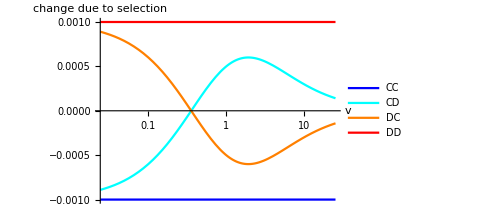

```mathematica
LogLinearPlot[{
-1/8 cc μμ,(μμ (bb νν (2+νν)-cc (3+νν (3+νν))))/(8 (1+νν)^2 (3+νν)),-(μμ (bb νν (2+νν)-cc (3+νν (3+νν))))/(8 (1+νν)^2 (3+νν)),1/8 cc μμ},{νν,0,0.625*nn},
AxesLabel->{"v","change due to selection"},PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625*nn},Automatic},ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red}]
```

### Plot relative abundances of strategies

See the SI for the derivation of the expressions plotted below.

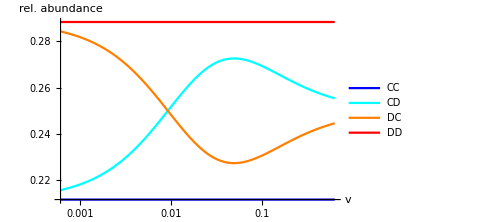

```mathematica
Clear[nn,ββ,pp,bb,cc,μμ,νν];
nn=40;uu=0.001;pp=0;ββ=0.001;cc=0.2;bb=1.0;μμ=nn*uu;

plot2=LogLinearPlot[{
1/4+ββ*(nn(1-uu))/uu ΔxCC[nn,bb,cc,ββ,pp,μμ,nn*vv],
1/4+ββ*(nn(1-uu))/uu ΔxCD[nn,bb,cc,ββ,pp,μμ,nn*vv],
1/4+ββ*(nn(1-uu))/uu ΔxDC[nn,bb,cc,ββ,pp,μμ,nn*vv],
1/4+ββ*(nn(1-uu))/uu ΔxDD[nn,bb,cc,ββ,pp,μμ,nn*vv]},{vv,0,0.625},
AxesLabel->{"v","rel. abundance"},PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625},Automatic},ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red}];
plot2
```

### Export data

```mathematica
Clear[n,β,p,u,v,params];
params={n->40,u->0.001,β->0.001,b->1.0,c->0.2}; (*note that pe is not needed*)

vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2/2}];
data=Flatten[
Table[{u/.params,v,
1/4+β*(n(1-u))/u ΔxCC[n,b,c,β,p,n*u,n*v]/.params,
1/4+β*(n(1-u))/u ΔxCD[n,b,c,β,p,n*u,n*v]/.params,
1/4+β*(n(1-u))/u ΔxDC[n,b,c,β,p,n*u,n*v]/.params,
1/4+β*(n(1-u))/u ΔxDD[n,b,c,β,p,n*u,n*v]/.params},{v,vs}],
0];
headers={"u","v","CC","CD","DC","DD"};
data=Prepend[data,headers];

filename="~/.julia/dev/CooperationPolarization2/analytics/calc_data_strat.csv"; (*change as needed*)
Export[filename,data]
```

~/.julia/dev/CooperationPolarization2/analytics/calc_data_strat.csv

```mathematica
data//MatrixForm
```

(u | v | CC | CD | DC | DD
0.001 | 0.001 | 0.211577 | 0.218119 | 0.281881 | 0.288423
0.001 | 0.00149535 | 0.211577 | 0.22106 | 0.27894 | 0.288423
0.001 | 0.00223607 | 0.211577 | 0.225126 | 0.274874 | 0.288423
0.001 | 0.0033437 | 0.211577 | 0.230551 | 0.269449 | 0.288423
0.001 | 0.005 | 0.211577 | 0.237427 | 0.262573 | 0.288423
0.001 | 0.00747674 | 0.211577 | 0.245538 | 0.254462 | 0.288423
0.001 | 0.0111803 | 0.211577 | 0.254211 | 0.245789 | 0.288423
0.001 | 0.0167185 | 0.211577 | 0.262312 | 0.237688 | 0.288423
0.001 | 0.025 | 0.211577 | 0.268551 | 0.231449 | 0.288423
0.001 | 0.0373837 | 0.211577 | 0.272001 | 0.227999 | 0.288423
0.001 | 0.0559017 | 0.211577 | 0.272503 | 0.227497 | 0.288423
0.001 | 0.0835925 | 0.211577 | 0.270662 | 0.229338 | 0.288423
0.001 | 0.125 | 0.211577 | 0.267465 | 0.232535 | 0.288423
0.001 | 0.186919 | 0.211577 | 0.26385 | 0.23615 | 0.288423
0.001 | 0.279508 | 0.211577 | 0.260464 | 0.239536 | 0.288423
0.001 | 0.417963 | 0.211577 | 0.257626 | 0.242374 | 0.288423
0.001 | 0.625 | 0.211577 | 0.255414 | 0.244586 | 0.288423)

### Plot Δx_CD as a function of b/c and ν

```mathematica
Plot3D[(b μ ν (2+ν)-c μ (3+ν (3+ν)))/(8 (1+ν)^2 (3+ν))/.{c->1,μ->1},{b,0,10},{ν,0,20},AxesLabel->{"b/c","ν(=Nv)","Δx_CD^sel"},ImageSize->Medium,ColorFunction->"ThermometerColors" ,PlotRange->{Automatic,Automatic,{-0.2,0.2}},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Solve[D[(b μ ν 2-c μ (3))/(8 (1)^2 (3))/.{c->1,μ->1},{ν}]==ν]
```

{{ν→b/12}}

## 4. Calculations with p = 1

### Compute y for p = 1

```mathematica
y2[n_,μ_,p_]:=(n/(2(n-1)))1/2+((n-2)/(2(n-1)))Integrate[ytau[μ,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]] (*ytau is from the p<1 calculation*)
```

```mathematica
yeval2[n_,μ_,ν_]=y2[n,μ,p]//FullSimplify;
ycalc2[n_,u_,v_]=y2[n,μ,p]/.{μ->n*u}//FullSimplify;
```

```mathematica
Print["y2 = ",yeval2[μ,ν]," or ",ycalc2[n,u,v]]
```

y2 = yeval2[μ,ν] or 1/4 (2+(-2+n)/((-1+n) (1+n u)))

```mathematica
yeval2[40,40*0.001,ν]
```

0.734221

### Compute z for p = 1

```mathematica
zeval2[n_,μ_,ν_]=-1/(n-1)//N;
zcalc2[n_,u_,v_]=-1/(n-1)//N;
```

```mathematica
zeval2[40,40*0.001,ν]//N
```

-0.025641

### Compute g for p = 1

```mathematica
g2[μ_,ν_,p_,n_]:=((n/2)/(n-1))*-1/2+((n/2-1)/(n-1))*Integrate[1*ytau[μ,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]  (*ytau is from the p<1 calculation*)
```

```mathematica
geval2[n_,μ_,ν_]=g2[μ,ν,p,n] // FullSimplify;
gcalc2[n_,u_,v_]=g2[μ,ν,p,n]/.{ν->n*v,μ->n*u}// FullSimplify;
```

```mathematica
Print["g2 = ",geval2[n,μ,ν]," or ",gcalc2[n,u,v]]
```

g2 = (n-2 (2+μ))/(4 (-1+n) (1+μ)) or (-4+n-2 n u)/(4 (-1+n) (1+n u))

```mathematica
(*geval2[n,μ,ν]-(1/(2(n-1))(-n/2+ (n/2-1)((μ+2)/(μ+1))))//FullSimplify (*check manual calculation*)*)
```

```mathematica
geval2[40,40*0.001,ν]
```

0.2214

### Compute h for p = 1

See the SI for the derivation.

```mathematica
h2[μ_,ν_,p_,n_]:=(-n/(4(n-1))+(n-4)/(4(n-1)))Integrate[ytau[μ,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
```

```mathematica
heval2[n_,μ_,ν_]=h2[μ,ν,p,n] // FullSimplify;
hcalc2[n_,u_,v_]=h2[μ,ν,p,n]/.{ν->n*v,μ->n*u}// FullSimplify;
```

```mathematica
Print["h2 = ",heval2[n,μ,ν]," or ",hcalc2[n,u,v]]
```

h2 = (2+μ)/(2-2 n+2 μ-2 n μ) or -(2+n u)/(2 (-1+n) (1+n u))

```mathematica
(*-1/(2(n-1))((μ+2)/(μ+1))-heval2[n,μ,ν]//FullSimplify(*check manual calculation*)*)
```

```mathematica
heval2[40,40*0.001,ν]
```

-0.0251479

### Export data for p = 1

```mathematica
Clear[n,β,p,u,v,params];
params={n->40,u->0.001,β->0.001};

(*generate a list of vs finer than the sims*)
vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2/2}];

(*compute y,z,g,h for each v*)
data=Flatten[
Table[{u/.params,v,
ycalc2[n,u,v]/.params,zcalc2[n,u,v]/.params,gcalc2[n,u,v]/.params,hcalc2[n,u,v]/.params},
{v,vs}],
0]; (*flatten into a data table*)
headers={"u","v","y","z","g","h"};
data=Prepend[data,headers];

filename="~/.julia/dev/CooperationPolarization2/analytics/calc_data_yzgh_p1.csv"; (*change as needed*)
Export[filename,data]
```

~/.julia/dev/CooperationPolarization2/analytics/calc_data_yzgh_p1.csv

```mathematica
data // MatrixForm
```

(u | v | y | z | g | h
0.001 | 0.001 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.00149535 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.00223607 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.0033437 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.005 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.00747674 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.0111803 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.0167185 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.025 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.0373837 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.0559017 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.0835925 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.125 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.186919 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.279508 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.417963 | 0.734221 | -0.025641 | 0.2214 | -0.0251479
0.001 | 0.625 | 0.734221 | -0.025641 | 0.2214 | -0.0251479)

### Computing the full bracketed terms for p = 1

We define the following functions to compute the original bracketed terms in (3):

```mathematica
Clear[nn,ββ,pp,bb,cc,μ,μμ,ν,νν];
ΔxCC2[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=1/nn xCCbracket2/.{n->nn,b->bb,c->cc,y->yeval2[nn,μ,ν]};
ΔxCD2[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=1/nn xCDbracket2/.{n->nn,b->bb,c->cc,z->zeval2[nn,μ,ν],g-> geval2[nn,μ,ν],h-> heval2[nn,μ,ν]};
ΔxDC2[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=1/nn xDCbracket2/.{n->nn,b->bb,c->cc,z->zeval2[nn,μ,ν],g-> geval2[nn,μ,ν],h->heval2[nn,μ,ν]};
ΔxDD2[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=1/nn xDDbracket2/.{n->nn,b->bb,c->cc,y-> yeval2[nn,μ,ν]};
```

The full expressions are

```mathematica
Clear[n,β,p,b,c,μ,ν];
FullSimplify[ΔxCC2[n,b,c,β,p,μ,ν]] 
FullSimplify[ΔxCD2[n,b,c,β,p,μ,ν]]
FullSimplify[ΔxDC2[n,b,c,β,p,μ,ν]] 
FullSimplify[ΔxDD2[n,b,c,β,p,μ,ν]]
```

-((b+c (-1+n)) (n+2 (-1+n) μ))/(16 n^2 (1+μ))

(b (-0.0625+0.0625 n) n+c n (0.0625+0.125 μ)+0.125 b μ-0.125 c μ)/(n^2 (1.+μ))

(b (0.0625-0.0625 n) n+c n (-0.0625-0.125 μ)-0.125 b μ+0.125 c μ)/(n^2 (1.+μ))

((b+c (-1+n)) (n+2 (-1+n) μ))/(16 n^2 (1+μ))

In the limit μ -> 0, we have

```mathematica
rules={d_?NumericQ+μ->d,d_?NumericQ+n->n,d_?NumericQ+μ^2-> d,d_?NumericQ +f_?NumericQ μ*k_-> d};
FullSimplify[ΔxCC2[n,b,c,β,p,μ,ν]]//.rules
FullSimplify[ΔxCD2[n,b,c,β,p,μ,ν]]//.rules
FullSimplify[ΔxDC2[n,b,c,β,p,μ,ν]]//.rules
FullSimplify[ΔxDD2[n,b,c,β,p,μ,ν]]//.rules
```

-((b+c n) (n+2 n μ))/(16 n^2)

(1. (b (-0.0625+0.0625 n) n+c n (0.0625+0.125 μ)+0.125 b μ-0.125 c μ))/n^2

(1. (b (0.0625-0.0625 n) n+c n (-0.0625-0.125 μ)-0.125 b μ+0.125 c μ))/n^2

((b+c n) (n+2 n μ))/(16 n^2)

### Plot changes due to selection for p = 1

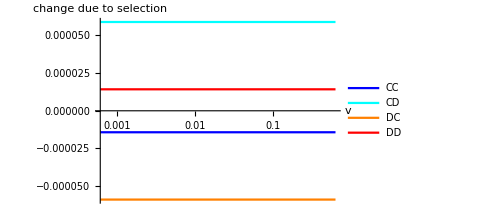

```mathematica
Clear[nn,ββ,pp,bb,cc,μμ,νν];
nn=40;uu=0.001;pp=0;ββ=0.001;cc=0.2;bb=1.0;μμ=nn*uu;

plot1=LogLinearPlot[{
ββ*ΔxCC2[nn,bb,cc,ββ,pp,μμ,nn*vv],
ββ*ΔxCD2[nn,bb,cc,ββ,pp,μμ,nn*vv],
ββ*ΔxDC2[nn,bb,cc,ββ,pp,μμ,nn*vv],
ββ*ΔxDD2[nn,bb,cc,ββ,pp,μμ,nn*vv]},{vv,0,0.625},
AxesLabel->{"v","change due to selection"},PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625},Automatic},ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red}];
plot1
```

### Plot relative abundances of strategies for p = 1

See the SI for the derivation of the expressions plotted below.

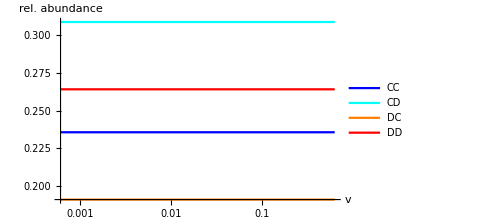

```mathematica
Clear[nn,ββ,pp,bb,cc,μμ,νν];
nn=40;uu=0.001;pp=0;ββ=0.001;cc=0.2;bb=1.0;μμ=nn*uu;

plot2=LogLinearPlot[{
1/4+ββ*(nn(1-uu))/(nn*uu)ΔxCC2[nn,bb,cc,ββ,pp,μμ,nn*vv],
1/4+ββ*(nn(1-uu))/(nn*uu)ΔxCD2[nn,bb,cc,ββ,pp,μμ,nn*vv],
1/4+ββ*(nn(1-uu))/(nn*uu)ΔxDC2[nn,bb,cc,ββ,pp,μμ,nn*vv],
1/4+ββ*(nn(1-uu))/(nn*uu)ΔxDD2[nn,bb,cc,ββ,pp,μμ,nn*vv]},{vv,0,0.625},
AxesLabel->{"v","rel. abundance"},PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625},Automatic},ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red}];
plot2
```

```mathematica
ΔxCD2[nn,bb,cc,ββ,pp,μμ,nn*vv]//FullSimplify
```

0.0589207

### Simplifying expressions for p = 1

```mathematica
subCC1={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subCC4={};
subCC2={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}] };
subCC3={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y)}; (*see the SI for definitions of y, z, g, h*)
subCC4={Subscript[s, {i,a}] Subscript[s, {i,d}] -> 1/4};
```

Then we can simplify the expression for CC as:

```mathematica
xCCbracket2p1=xCCbracket//.subCC1//.subCC2//.subCC3//.subCC4//FullSimplify
```

((b+c (-1+n)) (-1+n) (-1+y))/(4 n)

```mathematica
n*β*{xCCbracket3,xCDbracket3,xDCbracket3,xDDbracket3}/.{y->0.7391887,z->-0.02564103,g->0.2255689,h->-0.02538866,b->1.0,c->0.2,n->40,β->0.001}
```

{-0.0208649,0.100403,-0.100403,0.0208649}